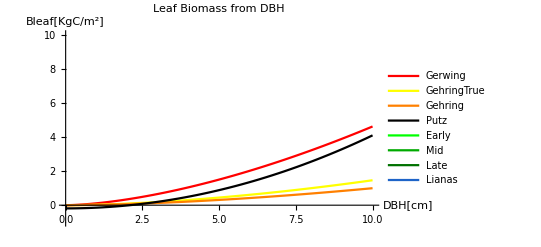

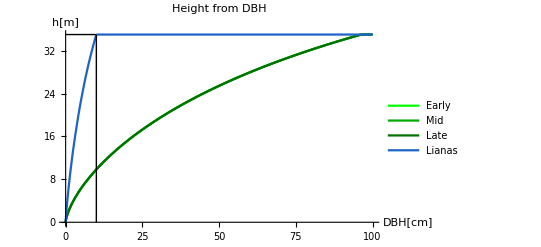

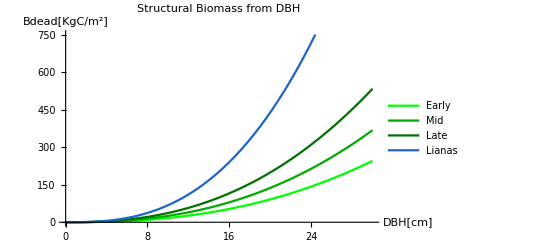

Part::partd: Part specification pftColor⟦1⟧ is longer than depth of object.

Part::partd: Part specification dbhCrit⟦1⟧ is longer than depth of object.

Part::partd: Part specification pftColor⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification pftColor⟦1⟧ is longer than depth of object.

Part::partd: Part specification dbhCrit⟦1⟧ is longer than depth of object.

Part::partd: Part specification pftColor⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
ClearAll["Global`*"]
b1Ht={0.0352,0.0352,0.0352,0.1136442};
b2Ht={0.694,0.694,0.694,0.8675};

(* This is the IALLOM=2 allometry, for used for the simulation with lianas*)
b1BlSmall={3.15389*^-1,4.73084*^-1,6.85972*^-1,3.15389*^-1};
b1BlLarge={3.15389*^-1,4.73084*^-1,6.85972*^-1,8.56000*^-2};
b2BlSmall={9.74949*^-1,9.74949*^-1,9.74949*^-1,9.74949*^-1};
b2BlLarge={9.74949*^-1,9.74949*^-1,9.74949*^-1,2.00000};
b1BlXu={0.024,0.016,0.046};
b2BlXu={1.75,2.12,1.93};

b1Cl={0.3106775,0.3106775,0.3106775,0.3106775};
b2Cl={1.098,1.098,1.098,1.098};

b1BsSmall={1.25446*^-1,1.88168*^-1,2.72844*^-1,0.2749};
b1BsLarge={1.29446*^-1,1.94169*^-1,2.81545*^-1,b1BsSmall[[4]]};
b2BsSmall={2.43236,2.43236,2.43236,2.69373};
b2BsLarge={2.42557,2.42557,2.42557,2.69373};

b1Ca={1.12573,1.12573,1.12573,1.12573};
b2Ca={1.05212,1.05212,1.05212,1.26254};

SLA={1.60179*^1,1.16448*^1,9.66342,1.20645*^1};

dbhAdult={1.00000*^1,1.00000*^1,1.00000*^1,4.48121};
dbhCrit={9.62578*^1,9.62578*^1,9.62578*^1,2.6*^1};
bleafAdult={1.48856,2.23284,3.23762,9.52538*^-1};
bdeadCrit={4.18656*^3,6.27984*^3,3.23762,3.00000*^1};

pftColor={Green,Darker[Green],Darker[Darker[Green]],RGBColor["#1E64C8"]};
XuColor={Red,Darker[Red],Darker[Darker[Red]]};
pftNames={"Early","Mid","Late","Lianas"};
XuNames={"TDF_D","TDF_BD","TDF_E"};

hgtRef=61.7;
C2B=2.0;


h2dbh[h_,ipft_,a_:1,b_:1]:=
If[ipft==4,(Log[hgtRef/(hgtRef-h)]/(a b1Ht[[ipft]]))^(1/(b b2Ht[[ipft]])),(Log[hgtRef/(hgtRef-h)]/b1Ht[[ipft]])^(1/b2Ht[[ipft]])];


dbh2h[dbh_,ipft_,a_:1,b_:1]:=Min[

If[ipft==4,hgtRef(1-Exp[-a b1Ht[[ipft]] dbh^(b b2Ht[[ipft]])]),hgtRef(1-Exp[-b1Ht[[ipft]] dbh^b2Ht[[ipft]]])],35];


dbh2bd[dbh_,ipft_]:=
Piecewise[{{b1BsSmall[[ipft]]/C2B dbh^b2BsSmall[[ipft]], dbh≤ dbhCrit[[ipft]]}, {b1BsLarge[[ipft]]/C2B dbh^b2BsLarge[[ipft]], True}}];


bd2dbh[bdead_,ipft_]:=
Piecewise[{{((bdead C2B)/b1BsSmall[[ipft]])^(1/b2BsSmall[[ipft]]), bdead≤bdeadCrit[[ipft]]}, {((bdead C2B)/b1BsLarge[[ipft]])^(1/b2BsLarge[[ipft]]), True}}];


size2bl[dbh_,ipft_,a_:b1BlSmall[[4]],b_:b2BlSmall[[4]],c_:b1BlLarge[[4]],d_:b2BlLarge[[4]]]:=
If[ipft≠4,Piecewise[{{b1BlSmall[[ipft]]/C2B Min[dbh,dbhCrit[[ipft]]]^b2BlSmall[[ipft]], dbh<dbhAdult[[ipft]]}, {b1BlLarge[[ipft]]/C2B Min[dbh,dbhCrit[[ipft]]]^b2BlLarge[[ipft]], True}}],
                         Piecewise[{{a/C2B Min[dbh,dbhCrit[[ipft]]]^b, dbh<dbhAdult[[ipft]]}, {c/C2B Min[dbh,dbhCrit[[ipft]]]^d-0.1538, True}}]];

size2blXu[dbh_,ipft_]:=
Piecewise[{{b1BlXu[[ipft]]/C2B Min[dbh,dbhCrit[[ipft]]]^b2BlXu[[ipft]], dbh<dbhAdult[[ipft]]}, {b1BlXu[[ipft]]/C2B Min[dbh,dbhCrit[[ipft]]]^b2BlXu[[ipft]], True}}];




bl2dbh[bleaf_,ipft_,a_:b1BlSmall[[4]],b_:b2BlSmall[[4]],c_:b1BlLarge[[4]],d_:b2BlLarge[[4]]]:=
If[ipft≠4,Piecewise[{{((bleaf C2B)/b1BlSmall[[ipft]])^(1/b2BlSmall[[ipft]]), bleaf<bleafAdult[[ipft]]}, {((bleaf C2B)/b1BlLarge[[ipft]])^(1/b2BlLarge[[ipft]]), True}}],
                         Piecewise[{{((bleaf C2B)/a)^(1/b), bleaf<bleafAdult[[ipft]]}, {((bleaf C2B)/c)^(1/d), True}}]];


dbh2ca[dbh_,ipft_,a_:b2Ca[[4]]]:=If[ipft==4,Min[b1Ca[[ipft]] Min[dbh,
dbhCrit[[ipft]]]^a,
loclai[dbh,ipft]],
Min[b1Ca[[ipft]] Min[dbh,
dbhCrit[[ipft]]]^b2Ca[[ipft]],
loclai[dbh,ipft]]];



putzbl[dbh_]:=(0.0856 dbh^2-0.376)/C2B;

GerwingBl[dbh_]:=0.110661 dbh^1.62;

GehringBl[dbh_]:=(0.04065 dbh^1.69)/C2B;

GehringBl2[dbh_]:=4.15*10^-4(0.02 dbh^2+12.35dbh)^1.69;

loclai[dbh_,ipft_]:=SLA[[ipft]]*size2bl[dbh,ipft];

CrownLength[h_,ipft_]:=Max[0.05,b1Cl[[ipft]] h^b2Cl[[ipft]]];


(*Text[Style["Piecewise[{{b1BlSmall[[ipft]]/C2B*dbh^b2BlSmall, dbh<dbhAdult[[ipft]]}, {b1BlLarge[[ipft]]/C2B*dbh^b2BlLarge, True}}]", 24]]
dbh2ca[1,2,1]*)


(*************************************************** H2DBH *************************************************)
Manipulate[
Grid[{{"short range","long range"},{
Plot[Evaluate@Table[h2dbh[h,ipft,a,b],{ipft,1,4}],{h,0.0,3.0},AxesLabel->{"h[m]","DBH[cm]"},PlotStyle->pftColor,ImageSize->400],
Plot[Evaluate@Table[h2dbh[h,ipft,a,b],{ipft,1,4}],{h,0.0,40.0},AxesLabel->{"h[m]","DBH[cm]"},PlotStyle->pftColor,ImageSize->400]}}],
{{a,1.},0.1,10.0,Appearance->"Labeled"},{{b,1.},0.1,10.0,Appearance->"Labeled"},FrameLabel->{{None,None},{None,"DBH(height)"}}]
(***********************************************************************************************************)

(************************************************** DBH2H **************************************************)
Manipulate[
Grid[{{"short range","long range"},{
Plot[Evaluate@Table[dbh2h[dbh,ipft,a,b],{ipft,1,4}],{dbh,0.0,2.0},AxesLabel->{"DBH[cm]","h[m]"},PlotStyle->pftColor,ImageSize->400],
Plot[Evaluate@Table[dbh2h[dbh,ipft,a,b],{ipft,1,4}],{dbh,0.0,100.0},AxesLabel->{"DBH[cm]","h[m]"},PlotStyle->pftColor,ImageSize->400]}}],
{{a,1.},0.1,10.0,Appearance->"Labeled"},{{b,1.},0.1,10.0,Appearance->"Labeled"},FrameLabel->{{None,None},{None,"height(DBH)"}}]
(***********************************************************************************************************)

(************************************************** DBH2CA *************************************************)
Manipulate[
Grid[{{"short range","long range"},{
Plot[Evaluate@Table[dbh2ca[dbh,ipft,a],{ipft,1,4}],{dbh,0.0,2.0},AxesLabel->{"dbh[cm]","CA[m^2]"},PlotStyle->pftColor,ImageSize->400],
Plot[Evaluate@Table[dbh2ca[dbh,ipft,a],{ipft,1,4}],{dbh,0.0,30.0},AxesLabel->{"dbh[cm]","Ca[m^2]"},PlotStyle->pftColor,ImageSize->400]}}],
{{a,b2Ca[[4]]},0.8b2Ca[[4]],1.2b2Ca[[4]],Appearance->"Labeled"},FrameLabel->{{None,None},{None,"DBH(canopyArea)"}}]
(***********************************************************************************************************)

(************************************************** SIZE2BL ************************************************)

Manipulate[
Legended[
Grid[{{"short range","long range"},{
Plot[Evaluate@Flatten@{GehringBl[dbh],putzbl[dbh],Table[size2bl[dbh,ipft,a,b,c,d],{ipft,1,4}]},{dbh,0.0,11.0},
PlotStyle->Flatten[{Orange,Black,pftColor}],
Exclusions->None,
PlotRange->{{0,11},{-1,5}},
AxesLabel->{"DBH[cm]","Bleaf[KgC/m2]"},
ImageSize->400],
{GehringBl,funcs,ControlType->TogglerBar}
Plot[Evaluate@Flatten@{GehringBl[dbh],putzbl[dbh],Table[size2bl[dbh,ipft,a,b,c,d],{ipft,1,4}]},{dbh,0.0,120.0},
AxesLabel->{"DBH[cm]","Bleaf[KgC/m2]"},
PlotStyle->Flatten[{Orange,Black,pftColor}],
Exclusions->None,
PlotRange->{{0,120},{0,40}},
ImageSize->400]}}],Placed[LineLegend[Flatten[{Orange,Black,pftColor}],Flatten[{"Gehring","Putz",pftNames}],LegendLayout->"Row"],Below]],
{{a,b1BlSmall[[4]],"b1Bl_small"},0.7b1BlSmall[[4]],1.3b1BlSmall[[4]],Appearance->"Labeled"},
{{b,b2BlSmall[[4]],"b2Bl_small"},0.7b2BlSmall[[4]],1.3b2BlSmall[[4]],Appearance->"Labeled"},
{{c,b1BlLarge[[4]],"b2Bl_large"},0.7b1BlLarge[[4]],1.3b1BlLarge[[4]],Appearance->"Labeled"},{{d,b2BlLarge[[4]],"b2Bl_large"},0.7b2BlLarge[[4]],1.3b2BlLarge[[4]],Appearance->"Labeled"},
FrameLabel->{{None,None},{None,"Bleaf(DBH)"}}]

funcs=Thread[
Evaluate@Flatten@{GerwingBl[dbh],
GehringBl2[dbh],
GehringBl[dbh],
putzbl[dbh],
Table[size2bl[dbh,ipft,a,b,c,d],{ipft,1,4}],
Table[size2blXu[dbh,ipft],{ipft,1,3}]
}->Flatten[{"Gerwing","GheringCorrected","Ghering","Putz",pftNames,XuNames}]];

Manipulate[
Legended[
Grid[{{"short range","long range"},{
Plot[fs,{dbh,0.0,8.0},
PlotStyle->Flatten[{Orange,Black,pftColor,XuColor}],
Exclusions->None,
PlotRange->{{0,8},{0,3}},
AxesLabel->{"DBH[cm]","Bleaf[KgC]"},
ImageSize->400],
Plot[fs,{dbh,0.0,110.0},
AxesLabel->{"DBH[cm]","Bleaf[KgC]"},
PlotStyle->Flatten[{Orange,Black,pftColor}],
Exclusions->None,
PlotRange->{{0,110},{0,40}},
ImageSize->400]}}],
Placed[LineLegend[Flatten[{Yellow,Orange,Purple,Black,pftColor,XuColor}],
Flatten[{"Gerwing","GheringCorrected","Ghering","Putz",pftNames,XuNames}],
LegendLayout->"Row"],
Below]],
{{a,b1BlSmall[[4]],"b1Bl_small"},0.7b1BlSmall[[4]],1.3b1BlSmall[[4]],Appearance->"Labeled"},
{{b,b2BlSmall[[4]],"b2Bl_small"},0.7b2BlSmall[[4]],1.3b2BlSmall[[4]],Appearance->"Labeled"},
{{c,b1BlLarge[[4]],"b2Bl_large"},0.7b1BlLarge[[4]],1.3b1BlLarge[[4]],Appearance->"Labeled"},{{d,b2BlLarge[[4]],"b2Bl_large"},0.7b2BlLarge[[4]],1.3b2BlLarge[[4]],Appearance->"Labeled"},
{fs,funcs,ControlType->TogglerBar},
FrameLabel->{{None,None},{None,"Bleaf(DBH)"}}]

(***********************************************************************************************************)

(************************************************* BL2DBH **************************************************)
(*Manipulate[
Grid[{{"short range","long range"},{
Plot[Evaluate@Table[bl2dbh[bleaf,ipft,a,b,c,d],{ipft,1,4}],{bleaf,0.0,3.0},AxesLabel->{"Bleaf[KgC/m2]","DBH[cm]"},
PlotStyle->pftColor,
ImageSize->400,
Exclusions->None],
Plot[Evaluate@Table[bl2dbh[bleaf,ipft,a,b,c,d],{ipft,1,4}],{bleaf,0.0,20.0},AxesLabel->{"Bleaf[KgC/m2]","DBH[cm]"},
PlotStyle->pftColor,
ImageSize->400,
Exclusions->None]}}],
{{a,b1BlSmall[[4]],"b1Bl_small"},0.7b1BlSmall[[4]],1.3b1BlSmall[[4]],Appearance->"Labeled"},
{{b,b2BlSmall[[4]],"b2Bl_small"},0.7b2BlSmall[[4]],1.3b2BlSmall[[4]],Appearance->"Labeled"},
{{c,b1BlLarge[[4]],"b2Bl_large"},0.7b1BlLarge[[4]],1.3b1BlLarge[[4]],Appearance->"Labeled"},{{d,b2BlLarge[[4]],"b2Bl_large"},0.7b2BlLarge[[4]],1.3b2BlLarge[[4]],Appearance->"Labeled"},
FrameLabel->{{None,None},{None,"DBH (Bleaf)"}}]*)
(***********************************************************************************************************)

(*********************************************** SIZE2BL XU ************************************************)
Legended[
Plot[Evaluate@Flatten@{GerwingBl[dbh],GehringBl2[dbh],GehringBl[dbh],putzbl[dbh],Table[size2blXu[dbh,ipft,b1BlSmall[[4]],b2BlSmall[[4]],b1BlLarge[[4]],b2BlLarge[[4]]],{ipft,1,3}]},{dbh,0.0,10.0},
PlotStyle->Flatten[{Red,Yellow,Orange,Black,pftColor}],
Exclusions->None,
PlotRange->{{0,10},{-1,10}},
AxesLabel->{"DBH[cm]","Bleaf[KgC/m^2]"},
ImageSize->400, PlotLabel->"Leaf Biomass from DBH"],
Placed[LineLegend[Flatten[{Red,Yellow,Orange,Black,pftColor}],Flatten[{"Gerwing","GehringTrue","Gehring","Putz",pftNames}],LegendLayout->"Row"],Below]]
(***********************************************************************************************************)

(*********************************************** DBH2H *****************************************************)
Legended[
Plot[Evaluate@Table[dbh2h[dbh,ipft,1,1],{ipft,1,4}],{dbh,0.0,100.0},AxesLabel->{"DBH[cm]","h[m]"},
Epilog->{Line[{{10,0},{10,35}}],Line[{{0,35},{10,35}}]},
PlotStyle->pftColor,ImageSize->400, PlotLabel->"Height from DBH"],
Placed[LineLegend[Flatten[pftColor],Flatten[pftNames],LegendLayout->"Row"],Below]]
(***********************************************************************************************************)

(************************************************ DBH2BD ***************************************************)
Legended[
Plot[Evaluate@Table[dbh2bd[dbh,ipft],{ipft,1,4}],{dbh,0.0,30.0},AxesLabel->{"DBH[cm]","Bdead[KgC/m^2]"},PlotStyle->pftColor,ImageSize->400, PlotLabel->"Structural Biomass from DBH"],
Placed[LineLegend[Flatten[pftColor],Flatten[pftNames],LegendLayout->"Row"],Below]]

(* p is a constant of the ellipsoid shape *)
(* dbhMax is the maximum allowed diameter *)

p:=1.6
dbhMax:=Max[dbhCrit]

(* EllipsoidSide computes the half height of an ellipsoid given a certain area and a certain minor
side (we also assume the two minor sides are equal a=b). Also we assume that the relevant area
ti draw the canopy is only the part facing uppwards, that is A->A/2. This is also made to get a
better graph...
*)
EllipsoidSide[A_,c_]:= b/.NSolve[b^(2p)+ 2(b c)^p==3(A/(2π))^p,b,Reals][[1]]

(* Minor and Major sides of the ellipsoid *)
MyMinor[dbh_,ipft_]:=EllipsoidSide[dbh2ca[dbh,ipft],(CrownLength[dbh2h[dbh,ipft],ipft]/2)]
MyMajor[dbh_,ipft_]:=CrownLength[dbh2h[dbh,ipft],ipft]/2

(* Center and bottom of the ellipsoid *)
EllipsoidCenter[dbh_,ipft_]:=dbh2h[dbh,ipft] - CrownLength[dbh2h[dbh,ipft],ipft]/2
EllipsoidBottom[dbh_,ipft_]:=dbh2h[dbh,ipft] - CrownLength[dbh2h[dbh,ipft],ipft]

(*SphereRadius[dbh_,ipft_]:= 5*size2bl[10*dbh,ipft]
SphereCenter[dbh_,ipft_]:=dbh2hM[dbh,ipft,1,1]- SphereRadius[dbh,ipft]*)

BoxX:=Max[Table[2*MyMinor[dbhMax,ipft],{ipft,1,4}]];
BoxY:=BoxX;
BoxZ:=dbh2h[dbhMax,1,1,1];

Manipulate[
Table[
Show[
Graphics3D[{pftColor[[ipft]],Opacity[1.0],Ellipsoid[{BoxX/2,BoxY/2,EllipsoidCenter[dbh,ipft]},{MyMinor[dbh,ipft],MyMinor[dbh,ipft],MyMajor[dbh,ipft]}]},PlotRange->{{0,BoxX},{0,BoxY},{0,BoxZ}},
ViewPoint->Front,
ImageSize->100,
Axes->True],
Graphics3D[{Brown,Cylinder[{{BoxX/2,BoxY/2,0},{BoxX/2,BoxY/2,EllipsoidBottom[dbh,ipft]}},Min[dbh,dbhCrit[[ipft]]] / 200.0(* we have to divide by 2 to get the radius and by 100 to get it in m *)]}]
],{ipft,1,4}]
,{{dbh,80,"dbh[cm]"},2,dbhMax,Appearance->"Labeled"}
]
```